```mathematica
Clear["Global`*"]
(*Needs["PhysicalConstants`"]*)
ϵ[ω_]:=ϵinf-ωp^2/(ω^2+1*ⅈ*γ*ω)
j[L_,z_]:=FunctionExpand[SphericalBesselJ[L,z]]
h[L_,z_]:=FunctionExpand[SphericalHankelH2[L,z]]
LHS[L_,z_]:=D[z*j[L,z],z]/(ϵp*j[L,z])
LHSexp[L_,z_,n_]:=Normal[Series[LHS[L,z],{z,0,n}]]
RHS[L_,z_]:=D[z*h[L,z],z]/(ϵb*h[L,z])
RHSexp[L_,z_,n_]:=Normal[Series[RHS[L,z],{z,0,n}]]
LHSexp[1,zp,2]
RHSexp[1,z0,2]
```

2/ϵp-zp^2/(5 ϵp)

-1/ϵb+z0^2/ϵb

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

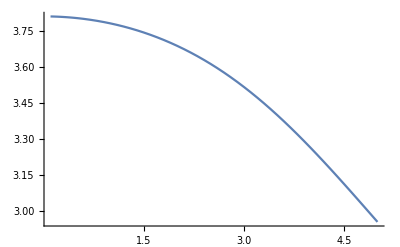

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

```mathematica
LHSb=LHSexp[1,zp,2]/.ϵp->ϵ[ω]/.zp->(a*ω/c)*Sqrt[ϵ[ω]];
RHSb=RHSexp[1,z0,2]/.z0->(a*ω/c)*Sqrt[ϵb];
ϵb=1;
ϵinf=3.77;
ωp=9.15;
γ=0.05;
c=2*10^(-7);
LHSb==RHSb;
-ω/.Solve[LHSb==RHSb,ω][[2]];
Plot[-Re[ω/.Solve[LHSb==RHSb,ω][[2]]],{a,1*10^(-9),50*10^(-9)},PlotRange->Full]
Table[-Re[ω/.Solve[LHSb==RHSb,ω][[2]]],{a,1*10^(-9),50*10^(-9),1*10^(-9)}];
Export["mie_omegas_water.txt",Table[-Re[ω/.Solve[LHSb==RHSb,ω][[2]]],{a,1*10^(-9),50*10^(-9),1*10^(-9)}]];
```

```mathematica
LHSexp[1,zp,2]
```

2/ϵp-zp^2/(5 ϵp)

```mathematica
RHSexp[1,z0,2]
```

-1+z0^2

```mathematica
LHSb=LHSexp[1,zp,2]/.ϵp->ϵ[ω]/.zp->(a*ω/c)*Sqrt[ϵ[ω]]
RHSb=RHSexp[1,z0,2]/.z0->(a*ω/c)*Sqrt[ϵb]
```

-200000000000/9 a^2 ω^2+2/(5.7-82.81/(0.+ω^2))

-1+(1000000000000 a^2 ω^2)/9